```mathematica
Clear["Global`*"]
```

# Derivation of Miller equations

## for “Available energy of trapped electrons in Miller tokamak equilibria”

R.J.J. Mackenbach

## Available Energy

### Derivation of omnigeneous integral

Let us denote the integral of (2.2)

```mathematica
Iz=FullSimplify[Integrate[8/(3 √π)*Exp[-z] z^(3/2)*Ramp[c0-c1*z],{z,0,∞}]]
```

Piecewise[{{2 c0-5 c1, c1≤0&&c0≥0}, {(2 √(c0/c1) (4 c0+15 c1) ⅇ^(-c0/c1))/(3 √π)+(2 c0-5 c1) Erf[√(c0/c1)], c0≥0&&c1>0}, {(ⅇ^(-c0/c1) (-8 c0 √(c0/c1)-30 c0 √(c1/c0)+3 (2 c0-5 c1) ⅇ^(c0/c1) √π Erfc[√(c0/c1)]))/(3 √π), c0<0&&c1<0}, {0, True}}]

which gives the results given in (2.3), (2.6), and (2.7).

## Local equilibrium construction

Here we calculate the various functions entering into the geometry calculations

### Lists for replacing and assumptions

Let us define some lists, useful for plotting and comparing against Miller.

```mathematica
FunctionToVarList={R0[r]->R0,δ[r]->δ,κ[r]->κ,θ->t}
ReplaceMiller={δ'[r]->sδ*(√(1-δ^2))/r,κ'[r]->sκ*κ/r,R0'[r]->dR0dr,δ[r]->δ,κ[r]->κ,R0[r]->R0}
MillerPaper={κ->1.66,r->1/3.17,δ->0.416,sκ->0.70,sδ->1.37,dR0dr->-0.354,R0->1.0}
sαList={δ'[r]->0,κ'[r]->0,R0'[r]->0,δ[r]->0,κ[r]->1,R0[r]->R0,r->ϵ*R0,sκ->0,sδ->0,δ->0,dR0dr->0,κ->1}
```

{R0[r]→R0,δ[r]→δ,κ[r]→κ,θ→t}

{δ'[r]→(sδ √(1-δ^2))/r,κ'[r]→(sκ κ)/r,R0'[r]→dR0dr,δ[r]→δ,κ[r]→κ,R0[r]→R0}

{κ→1.66,r→0.315457,δ→0.416,sκ→0.7,sδ→1.37,dR0dr→-0.354,R0→1.}

{δ'[r]→0,κ'[r]→0,R0'[r]→0,δ[r]→0,κ[r]→1,R0[r]→R0,r→R0 ϵ,sκ→0,sδ→0,δ→0,dR0dr→0,κ→1}

We also set assumptions on the Miller parameters:

```mathematica
$Assumptions:={r>0,κ>0,ϵ>0,R0>0,Element[θ,Reals]}
```

### Derivation of geometry

Let us first define the geometry components, i.e. the cross-section defining the flux-surface.

```mathematica
Rs=R0[r]+r*Cos[θ+(ArcSin[δ[r]]*Sin[θ])]
Zs=κ[r]*r*Sin[θ]
```

r Cos[θ+ArcSin[δ[r]] Sin[θ]]+R0[r]

r Sin[θ] κ[r]

Our next step is to calculate components sin(u) and cos(u).

```mathematica
sinu=FullSimplify[D[Zs,θ]*1/(√(D[Zs,θ]^2+D[Rs,θ]^2))/.ReplaceMiller]
cosu=FullSimplify[-D[Rs,θ]*1/(√(D[Zs,θ]^2+D[Rs,θ]^2))/.ReplaceMiller]
```

(κ Cos[θ])/(√(κ^2 Cos[θ]^2+(1+ArcSin[δ] Cos[θ])^2 Sin[θ+ArcSin[δ] Sin[θ]]^2))

((1+ArcSin[δ] Cos[θ]) Sin[θ+ArcSin[δ] Sin[θ]])/(√(κ^2 Cos[θ]^2+(1+ArcSin[δ] Cos[θ])^2 Sin[θ+ArcSin[δ] Sin[θ]]^2))

Lets calculate the radius of curvature from this u, Eq. (4) in Miller, and the standard manner. We need dl/dθ for this

```mathematica
lθ=FullSimplify[√(D[Zs,θ]^2+D[Rs,θ]^2)/.ReplaceMiller]
dudθ=FullSimplify[D[sinu,θ]/cosu];
dudl=FullSimplify[dudθ/lθ];
RcMiller=FullSimplify[1/dudl];
Rc=-FullSimplify[((D[Rs,θ]^2+D[Zs,θ]^2)^(3/2))/(D[Rs,{θ,1}]*D[Zs,{θ,2}]-D[Rs,{θ,2}]*D[Zs,{θ,1}])/.ReplaceMiller]
FullSimplify[Rc==RcMiller]
```

r √(κ^2 Cos[θ]^2+(1+ArcSin[δ] Cos[θ])^2 Sin[θ+ArcSin[δ] Sin[θ]]^2)

-(r (κ^2 Cos[θ]^2+(1+ArcSin[δ] Cos[θ])^2 Sin[θ+ArcSin[δ] Sin[θ]]^2)^(3/2))/(κ (Cos[ArcSin[δ] Sin[θ]]+ArcSin[δ] Cos[θ]^2 (2+ArcSin[δ] Cos[θ]) Cos[θ+ArcSin[δ] Sin[θ]]))

True

Next, we calculate the poloidal magnetic field, for which we need ∇r. Expressions for this may be found in “A unified method for operator evaluation in local Grad–Shafranov plasma equilibria” (2009), see Eq. (39).

```mathematica
sqrtgθθ=lθ
divr=FullSimplify[sqrtgθθ/(D[Rs,r]*D[Zs,θ]-D[Rs,θ]*D[Zs,r])/.ReplaceMiller]
bp=divr/(Rs/R0)/.ReplaceMiller
bt=R0/Rs/.ReplaceMiller
bs=√(((γ*ϵ)/q)^2 bp^2+bt^2)
```

r √(κ^2 Cos[θ]^2+(1+ArcSin[δ] Cos[θ])^2 Sin[θ+ArcSin[δ] Sin[θ]]^2)

(√(κ^2 Cos[θ]^2+(1+ArcSin[δ] Cos[θ])^2 Sin[θ+ArcSin[δ] Sin[θ]]^2))/(κ Cos[θ] (dR0dr+Cos[θ+ArcSin[δ] Sin[θ]])+κ (1+sκ-sδ Cos[θ]+(1+sκ) ArcSin[δ] Cos[θ]) Sin[θ] Sin[θ+ArcSin[δ] Sin[θ]])

(R0 √(κ^2 Cos[θ]^2+(1+ArcSin[δ] Cos[θ])^2 Sin[θ+ArcSin[δ] Sin[θ]]^2))/((R0+r Cos[θ+ArcSin[δ] Sin[θ]]) (κ Cos[θ] (dR0dr+Cos[θ+ArcSin[δ] Sin[θ]])+κ (1+sκ-sδ Cos[θ]+(1+sκ) ArcSin[δ] Cos[θ]) Sin[θ] Sin[θ+ArcSin[δ] Sin[θ]]))

R0/(R0+r Cos[θ+ArcSin[δ] Sin[θ]])

√(R0^2/(R0+r Cos[θ+ArcSin[δ] Sin[θ]])^2+(R0^2 γ^2 ϵ^2 (κ^2 Cos[θ]^2+(1+ArcSin[δ] Cos[θ])^2 Sin[θ+ArcSin[δ] Sin[θ]]^2))/(q^2 (R0+r Cos[θ+ArcSin[δ] Sin[θ]])^2 (κ Cos[θ] (dR0dr+Cos[θ+ArcSin[δ] Sin[θ]])+κ (1+sκ-sδ Cos[θ]+(1+sκ) ArcSin[δ] Cos[θ]) Sin[θ] Sin[θ+ArcSin[δ] Sin[θ]])^2))

Finally we write down the area of the enclosed flux-surface

```mathematica
dψtdθ=FullSimplify[(-2/π*(Zs/r)*D[(Rs/r),θ]/(Rs/R0)/.ReplaceMiller)/.{r->R0*ϵ}]
D[(Rs/r),θ]
Manipulate[Plot[(2  (1+ArcSin[δ] Cos[θ]) Sin[θ] Sin[θ+ArcSin[δ] Sin[θ]])/(π+π ϵ Cos[θ+ArcSin[δ] Sin[θ]]),{θ,0,2π}],{{δ,0},-1,1},{{ϵ,0},0,1}]
```

(2 κ (1+ArcSin[δ] Cos[θ]) Sin[θ] Sin[θ+ArcSin[δ] Sin[θ]])/(π+π ϵ Cos[θ+ArcSin[δ] Sin[θ]])

-((1+ArcSin[δ[r]] Cos[θ]) Sin[θ+ArcSin[δ[r]] Sin[θ]])

```mathematica
ψt=AsymptoticIntegrate[dψtdθ/2,{θ,0,2*π},{ϵ,0,1}]
```

(2 κ BesselJ[1,ArcSin[δ]])/ArcSin[δ]+(ϵ κ BesselJ[2,2 ArcSin[δ]])/(2 ArcSin[δ])

```mathematica
ψtnorm=Series[FullSimplify[ψt],{ϵ,0,1}]
reff0=Normal[Series[r*√ψtnorm,ϵ->0]]
reff=Normal[Series[r*(√ψtnorm)/reff0,{ϵ,0,1}]]
```

(2 κ BesselJ[1,ArcSin[δ]])/ArcSin[δ]+(κ BesselJ[2,2 ArcSin[δ]] ϵ)/(2 ArcSin[δ])+O[ϵ]^2

√2 r √κ √(BesselJ[1,ArcSin[δ]]/ArcSin[δ])

1+(ϵ BesselJ[2,2 ArcSin[δ]])/(8 BesselJ[1,ArcSin[δ]])

#### Plots

We verify that this is indeed the correct form by making a parametric plot:

```mathematica
PlotVars={Rs,Zs}/.FunctionToVarList
Manipulate[ParametricPlot[{R0+r Cos[t+ArcSin[δ] Sin[t]],r κ Sin[t]},{t,0,2π}],{R0,1,1},{{r,0.5},0,1},{{δ,0.5},-1,1},{{κ,1.5},0,2}]
```

{R0+r Cos[t+ArcSin[δ] Sin[t]],r κ Sin[t]}

Now plot Bp to check against Miller (1998). See Fig. 3.

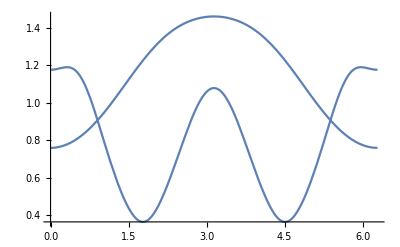

```mathematica
Plot[{bp,bt}/.MillerPaper,{θ,0,2π}]
```

Finally plot the dependence of the cross-sectional area on triangularity

```mathematica
Manipulate[Plot[√((2*BesselJ[1,ArcSin[δ]])/ArcSin[δ])*(1+(ϵ BesselJ[2,2 ArcSin[δ]])/(8 BesselJ[1,ArcSin[δ]])),{δ,-1,1},PlotRange->{0,1.5}],{ϵ,0,1}]
```

### The s-α limit

Now we calculate the s-α limit, taking elongation into account

```mathematica
sinusα=FullSimplify[D[Zs,θ]*1/(√(D[Zs,θ]^2+D[Rs,θ]^2))/.sαList];
Rssα=FullSimplify[Rs/R0/.sαList];
Bpssα=FullSimplify[bp/.sαList];
Btsα=FullSimplify[bt/.sαList];
Rcsα=FullSimplify[Rc/r/.sαList];
lθsα=FullSimplify[lθ/r/.sαList];
Bssα=FullSimplify[bs/.sαList];
fpR0=fpR0sol/.Solve[fpR0sol*q/γ-α/(2*ϵ)==σ,fpR0sol][[1]];
γ=FullSimplify[Integrate[FullSimplify[Normal[Series[1/(2π)*lθsα/(Rssα^2*Bpssα),{ϵ,0,1}]]],{θ,0,2π}]]
C1=FullSimplify[Integrate[FullSimplify[Normal[Series[1/(2π)*lθsα/(Rssα^3*Bpssα^2*Rcsα),{ϵ,0,1}]]],{θ,0,2π}]]
C2=FullSimplify[Integrate[FullSimplify[Normal[Series[1/(2π)*(lθsα*sinusα)/(Rssα^4*Bpssα^2),{ϵ,0,1}]]],{θ,0,2π}]]
C3=FullSimplify[Integrate[FullSimplify[Normal[Series[1/(2π)*lθsα/(Rssα^2*Bpssα^3),{ϵ,0,1}]]],{θ,0,2π}]]
C4=FullSimplify[Integrate[FullSimplify[Normal[Series[1/(2π)*lθsα/(Rssα^4*Bpssα^3),{ϵ,0,1}]]],{θ,0,2π}]]
ξ=FullSimplify[Integrate[FullSimplify[Normal[Series[(lθsα*Bssα)/Bpssα,{ϵ,0,1}]]],{θ,0,2π}]]
ξ2=FullSimplify[Integrate[FullSimplify[Normal[Series[lθsα/Bpssα,{ϵ,0,1}]]],{θ,0,2π}]]
```

1

-1

-ϵ

1

1

2 π

2 π

Solve for σ

```mathematica
Eqσ=s==(γ*ϵ^2)/q*fpR0-2/γ*C1-(2ϵ)/γ*C2-α/(2γ ϵ)C3+q/γ^2 C4*fpR0
EqσSeries=Normal[Series[Eqσ,{ϵ,0,0}]]
σsol=Solve[EqσSeries,σ][[1]]
```

s==2-α/(2 ϵ)+2 ϵ^2+(α+2 ϵ σ)/(2 ϵ)+(ϵ (α+2 ϵ σ))/(2 q^2)

s==2+σ

{σ→-2+s}

Now we calculate the magnetic field variations

```mathematica
rdbpdρ=Normal[Series[1/Rcsα-α/(2*ϵ*Bpssα)*(1/Rssα-Rssα)-σ/(Rssα*Bpssα)/.σsol,ϵ->0]]
rdbtdρ=Normal[Series[((γ*ϵ)/q)^2(σ+α/(2ϵ))*Rssα*Bpssα-ϵ sinusα/Rssα/.σsol,ϵ->0]]
rdbdρ=Normal[Series[(Btsα^2*rdbtdρ+((γ*ϵ)/q Bpssα)^2*rdbpdρ)/Bssα^2,ϵ->0]]
λB=Normal[Series[(1+ϵ*(1-2 k^2))/Rssα,{ϵ,0,1}]]
```

1-s+α Cos[θ]

ϵ (α/(2 q^2)-Cos[θ])

ϵ (α/(2 q^2)-Cos[θ])

1+ϵ (1-2 k^2-Cos[θ])

Finally expand the argument of the bounce-averaging operator

```mathematica
argument=Normal[Series[1/ϵ*(2*(1-λB)*(rdbdρ-rdbpdρ-1/Rcsα)-λB*rdbdρ)/(Bpssα*Rssα),ϵ->0]]
```

-α/(2 q^2)+Cos[θ]-2 (1-2 k^2-Cos[θ]) (s-α Cos[θ])

Now we do the bounce-averaging operation. Following appendix (A) we need to evaluate

```mathematica
const=2*√(2/ϵ)Limit[Integrate[((1-2*k^2*Sin[θ]^2)^0)/(√(1-k^2*Sin[θ]^2)),{θ,0,a}],{a->π/2},Direction->"FromBelow"]
cos=2*√(2/ϵ)Limit[Integrate[((1-2*k^2*Sin[θ]^2)^1)/(√(1-k^2*Sin[θ]^2)),{θ,0,a}],{a->π/2},Direction->"FromBelow"]/const
cos2=2*√(2/ϵ)Limit[Integrate[((1-2*k^2*Sin[θ]^2)^2)/(√(1-k^2*Sin[θ]^2)),{θ,0,a}],{a->π/2},Direction->"FromBelow"]/const
```

2 √2 √(1/ϵ) EllipticK[k^2]

(2 EllipticE[k^2]-EllipticK[k^2])/EllipticK[k^2]

((4-8 k^2) EllipticE[k^2]+(-1+4 k^2) EllipticK[k^2])/(3 EllipticK[k^2])

Do subs to find ωλ, check if same as Connor, Hastie, Martin

```mathematica
ωλ=(ExpandAll[argument]/.{Cos[θ]^2->cos2})/.{Cos[θ]->cos}
G1=ExpandAll[ωλ/2/.{α->0,s->0}]
G2=ExpandAll[(ωλ/2-G0)/(2s)/.{α->0}]
G3=ExpandAll[(ωλ/2-G0+α/(4 q^2))/(-α*2/3)/.{s->0}]
ωλ=-α/(2 q^2)+2*G1+4*s*G2-α 4/3 G3
```

-2 s+4 k^2 s-α/(2 q^2)+(2 EllipticE[k^2]-EllipticK[k^2])/EllipticK[k^2]+(2 s (2 EllipticE[k^2]-EllipticK[k^2]))/EllipticK[k^2]+(2 α (2 EllipticE[k^2]-EllipticK[k^2]))/EllipticK[k^2]-(4 k^2 α (2 EllipticE[k^2]-EllipticK[k^2]))/EllipticK[k^2]-(2 α ((4-8 k^2) EllipticE[k^2]+(-1+4 k^2) EllipticK[k^2]))/(3 EllipticK[k^2])

-1/2+EllipticE[k^2]/EllipticK[k^2]

-1+k^2-1/(4 s)-G0/(2 s)+EllipticE[k^2]/EllipticK[k^2]+EllipticE[k^2]/(2 s EllipticK[k^2])

1-k^2+3/(4 α)+(3 G0)/(2 α)-EllipticE[k^2]/EllipticK[k^2]+(2 k^2 EllipticE[k^2])/EllipticK[k^2]-(3 EllipticE[k^2])/(2 α EllipticK[k^2])

-α/(2 q^2)+2 (-1/2+EllipticE[k^2]/EllipticK[k^2])+4 s (-1+k^2-1/(4 s)-G0/(2 s)+EllipticE[k^2]/EllipticK[k^2]+EllipticE[k^2]/(2 s EllipticK[k^2]))-4/3 α (1-k^2+3/(4 α)+(3 G0)/(2 α)-EllipticE[k^2]/EllipticK[k^2]+(2 k^2 EllipticE[k^2])/EllipticK[k^2]-(3 EllipticE[k^2])/(2 α EllipticK[k^2]))

```mathematica
prefactor=2/3*3/16*2*(√2)/π
```

1/(2 √2 π)